## Bose-Hubbard model simulation

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<../mathematica/mps_base.m
```

### General definitions

```mathematica
SparseIdentityMatrix[d_]:=SparseArray[{i_,i_}->1,{d,d}]
```

```mathematica
SiteCreateOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],-1]
SiteAnnihilOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],1]
```

```mathematica
NumberOp[M_]:=DiagonalMatrix[Range[0,M]]
```

```mathematica
Z[H_,β_]:=Norm[MatrixExp[-β/2 H],"Frobenius"]^2
```

```mathematica
(* construct Bose-Hamiltonian with open boundary conditions *)
HBose[t_,U_,μ_,M_,1]:=U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M]
HBose[t_,U_,μ_,M_,L_]:=-t Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],SiteCreateOp[M],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-l-1)]]+KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],SiteAnnihilOp[M],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-l-1)]],{l,1,L-1}]+Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M],SparseIdentityMatrix[(M+1)^(L-l)]],{l,1,L}]
```

### Simulation parameters

```mathematica
(* kinetic hopping parameter *)
Subscript[tH, val]=1;
```

```mathematica
(* interaction strength *)
Subscript[U, val]=5;
```

```mathematica
(* chemical potential *)
Subscript[μ, val]=1/7;
```

```mathematica
(* number of lattice sites *)
Subscript[L, val]=5;
```

```mathematica
(* single site occupation number cut-off *)
Subscript[M, val]=2;
```

```mathematica
(* inverse temperature *)
Subscript[β, val]=3/5;
```

```mathematica
Subscript[t, list]=Range[0,5,1/4];
Length[%]
```

21

### Energy correlations

```mathematica
χC[A_,B_,H_,β_,t_]:=Module[{tA=t/2,tB=t/2,ρβ=MatrixExp[-β/2 H]},1/Z[H,β] Tr[(MatrixExp[ⅈ tB H].ρβ.B.MatrixExp[-ⅈ tB H]).(MatrixExp[-ⅈ tA H].A.ρβ.MatrixExp[ⅈ tA H])]]
```

```mathematica
BondEnergyOp[j_,t_,U_,M_,L_]:=-t(KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],SiteCreateOp[M],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]+KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],SiteAnnihilOp[M],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]])+U/4(KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1]),SparseIdentityMatrix[(M+1)^(L-j)]]+KroneckerProduct[SparseIdentityMatrix[(M+1)^j],NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1]),SparseIdentityMatrix[(M+1)^(L-j-1)]])
```

```mathematica
Subscript[fn, import]="../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"_energy/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]];
```

```mathematica
(* read simulation results from disk *)
Subscript[ee, corr]=Import[Subscript[fn, import]<>"_ee_corr.dat","Complex128"]
Dimensions[%]
```

{0.175897+0. ⅈ,0.165757+0.0255007 ⅈ,0.226369+0.0904831 ⅈ,0.33879+0.0567058 ⅈ,0.327393-0.0276516 ⅈ,0.270943+0.00943057 ⅈ,0.330655+0.0783623 ⅈ,0.422724+0.0553074 ⅈ,0.439427-0.00947063 ⅈ,0.393238-0.0253871 ⅈ,0.387987+0.0123731 ⅈ,0.421058-0.00600804 ⅈ,0.381384-0.0518869 ⅈ,0.323179-0.0255333 ⅈ,0.335502+0.00414329 ⅈ,0.333278-0.0192228 ⅈ,0.302058-0.00217585 ⅈ,0.323272+0.0313206 ⅈ,0.356852+0.0396069 ⅈ,0.403429+0.0421046 ⅈ,0.430286+0.000573886 ⅈ}

{21}

```mathematica
Subscript[i, site]=2;
Subscript[j, site]=4;
```

```mathematica
(* reference calculation *)
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],HB},HB=N[HBose[tH,U,μ,M,L]];Subscript[ee, corr,ref]=Table[χC[BondEnergyOp[Subscript[i, site],tH,U,M,L],BondEnergyOp[Subscript[j, site],tH,U,M,L],HB,β,t],{t,Subscript[t, list]}]]
```

{0.175939,0.16575+0.0254398 ⅈ,0.226317+0.0904531 ⅈ,0.338766+0.0567192 ⅈ,0.32742-0.0276448 ⅈ,0.270974+0.00939482 ⅈ,0.330654+0.0783271 ⅈ,0.422731+0.0552982 ⅈ,0.439432-0.00948452 ⅈ,0.393233-0.0253772 ⅈ,0.388021+0.0123733 ⅈ,0.421059-0.00603905 ⅈ,0.381374-0.0518603 ⅈ,0.323225-0.0255269 ⅈ,0.335511+0.00411187 ⅈ,0.333273-0.0192083 ⅈ,0.302085-0.00215338 ⅈ,0.32331+0.0313286 ⅈ,0.356889+0.0396006 ⅈ,0.403438+0.0420975 ⅈ,0.430301+0.00060354 ⅈ}

```mathematica
(* compare *)
Abs[Subscript[ee, corr]-Subscript[ee, corr,ref]]
```

{0.0000422895,0.0000613233,0.0000598064,0.0000271366,0.0000274675,0.0000468798,0.0000352469,0.0000115618,0.0000149548,0.0000109596,0.0000337056,0.0000310245,0.0000282596,0.000046542,0.0000328874,0.0000155626,0.0000352503,0.0000380522,0.0000374175,0.000011335,0.0000334599}

```mathematica
Subscript[plot, label]="Bose-Hubbard model with\nt_H="<>ToString[Subscript[tH, val]]<>", U="<>ToString[Subscript[U, val]]<>", μ="<>ToString[InputForm[Subscript[μ, val]]]<>", M="<>ToString[Subscript[M, val]]<>", L="<>ToString[Subscript[L, val]]<>", β="<>ToString[N[Subscript[β, val]]]<>"\nsites: i="<>ToString[Subscript[i, site]]<>", j="<>ToString[Subscript[j, site]];
```

```mathematica
Subscript[fn, export]="plots/"<>#<>"/"<>#<>"_"&[FileBaseName[NotebookFileName[]]];
```

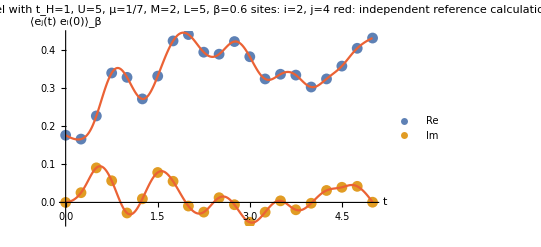

```mathematica
Show[ListPlot[{Transpose[{Subscript[t, list],Re[Subscript[ee, corr]]}],Transpose[{Subscript[t, list],Im[Subscript[ee, corr]]}]},AxesLabel->{"t","⟨e_j(t) e_i(0)⟩_β"},PlotLegends->{"Re","Im"},PlotLabel->Subscript[plot, label]<>"\nred: independent reference calculation"],ListLinePlot[{Transpose[{Subscript[t, list],Re[Subscript[ee, corr,ref]]}],Transpose[{Subscript[t, list],Im[Subscript[ee, corr,ref]]}]},PlotRange->{All,{-1,1}},InterpolationOrder->4,PlotStyle->ColorData[97][4]]]
Export[Subscript[fn, export]<>"ee_corr_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

### Virtual bond dimensions

```mathematica
Subscript[t, plot]=Range[0,5];
```

```mathematica
Subscript[t, idx]=Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]]
```

{1,5,9,13,17,21}

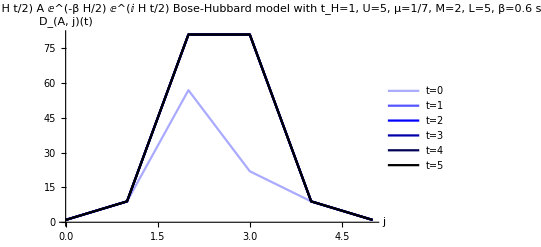

```mathematica
(* virtual bond dimension for 'A' operator *)
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@Partition[Import[Subscript[fn, import]<>"_DXA.dat","Integer64"],Subscript[L, val]+1]⟦Subscript[t, idx]⟧,AxesLabel->{"j","D_(A, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(-ⅈ H t/2) A ⅇ^(-β H/2) ⅇ^(ⅈ H t/2)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DA_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```

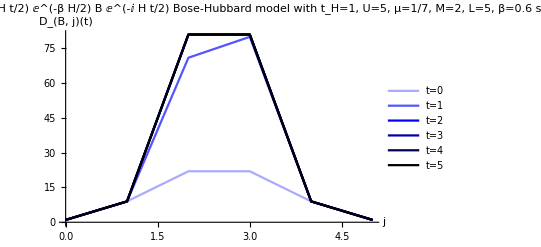

```mathematica
(* virtual bond dimension for 'B' operator *)
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@Partition[Import[Subscript[fn, import]<>"_DXB.dat","Integer64"],Subscript[L, val]+1]⟦Subscript[t, idx]⟧,AxesLabel->{"j","D_(B, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(ⅈ H t/2) ⅇ^(-β H/2) B ⅇ^(-ⅈ H t/2)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DB_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```

### Effective truncation weight

```mathematica
(* tolerance (truncation weight) for ⅇ^(-β H/2) *)
Norm[Partition[Import[Subscript[fn, import]<>"_tol_eff_beta.dat","Real64"],Subscript[L, val]-1]-10^-10]
```

0.

```mathematica
(* tolerance (truncation weight) for ⅇ^(-ⅈ H t/2) A ⅇ^(-β H/2) ⅇ^(ⅈ H t/2) *)
Norm[Partition[Import[Subscript[fn, import]<>"_tol_eff_A.dat","Real64"],Subscript[L, val]-1]-10^-10]
```

0.

```mathematica
(* tolerance (truncation weight) for ⅇ^(ⅈ H t/2) ⅇ^(-β H/2) B ⅇ^(-ⅈ H t/2) *)
Norm[Partition[Import[Subscript[fn, import]<>"_tol_eff_B.dat","Real64"],Subscript[L, val]-1]-10^-10]
```

0.